```mathematica
NSolve[{-ϕ[x]''-ϕ[x]^3/(1+ϕ[x]^2)==ω^2 ϕ[x],ϕ[10]==0,ϕ[-10]==0},{x,-10,10}]
```

NSolve::ivar: TraditionalForm`-10 is not a valid variable.

NSolve[{-ϕ(x)''-(ϕ(x))^3/((ϕ(x))^2+1)==ω^2 ϕ(x),ϕ(10)==0,ϕ(-10)==0},{x,-10,10}]

```mathematica
xmax=10;
xmin=-10;
dy0=Pi/10.; (* step size of the boundary condition at xmin *)
dy1=Pi/10.; (* step size of the boundary condition at xmax *)
tol=0.1; (* tolerance for non-zero derivativ at boundaries *)
PlotList={};
SolitonList={};
BCList={};

y0=0;
y1=-3Pi;
While[y0<0,
While[y1<7Pi,
Clear[error,y,x,c];
error[c_?NumericQ]:=(y[xmax]-y1)/.NDSolve[{y''[x]-Sin[y[x]]==0,y[xmin]==y0,y'[xmin]==c},y,{x,xmin,xmax},AccuracyGoal->10,PrecisionGoal->30][[1]];
c0=c/.FindRoot[error[c],{c,0}];

soln=NDSolve[{y''[x]-Sin[y[x]]==0,y[xmin]==0,y'[xmin]==c0},y,{x,xmin,xmax},AccuracyGoal->10,PrecisionGoal->30][[1]];

If[(Abs[soliton'[xmin]]<tol)&&(Abs[soliton'[xmax]]<tol),
AppendTo[BCList,{y0,y1}];
SolitonList=Append[SolitonList,soln];
PlotList=Append[PlotList,Plot[y[x]/.soln//Evaluate,{x,xmin,xmax},PlotRange->All]];
];

y1=y1+dy1;
];
y0=y0+dy0;
]
```

```mathematica
xmax=600;
xmin=-600;
dω=0.1; (* step size of the boundary condition at xmin *)
tol=0.1; (* tolerance for non-zero derivativ at boundaries *)
PlotList={};
SolitonList={};

y0=0.001;
y1=0.001;
ω=0;
While[ω<0.001,
Clear[error,y,x,c];
error[c_?NumericQ]:=(y[xmax]-y1)/.NDSolve[{-y''[x]-y[x]^3/(1+y[x]^2)==-ω^2 y[x],y[xmin]==y0,y'[xmin]==c},y,{x,xmin,xmax},AccuracyGoal->10,PrecisionGoal->30][[1]];
c0=c/.FindRoot[error[c],{c,0}];

soln=NDSolve[{-y''[x]-y[x]^3/(1+y[x]^2)==-ω^2 y[x],y[xmin]==y0,y'[xmin]==c0},y,{x,xmin,xmax},AccuracyGoal->10,PrecisionGoal->30][[1]];

SolitonList=Append[SolitonList,soln];
PlotList=Append[PlotList,Plot[y[x]/.soln//Evaluate,{x,xmin,xmax},PlotRange->All]];

ω=ω-dω;
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

NDSolve::ndtol: Tolerances requested by the AccuracyGoal and PrecisionGoal options could not be achieved at TraditionalForm`x == TraditionalForm`-575.693.

InterpolatingFunction::dmval: Input value TraditionalForm`{600} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndtol: Tolerances requested by the AccuracyGoal and PrecisionGoal options could not be achieved at TraditionalForm`x == TraditionalForm`-575.693.

InterpolatingFunction::dmval: Input value TraditionalForm`{600} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndtol: Tolerances requested by the AccuracyGoal and PrecisionGoal options could not be achieved at TraditionalForm`x == TraditionalForm`-575.691.

General::stop: Further output of NDSolve :: ndtol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{600} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

$Aborted

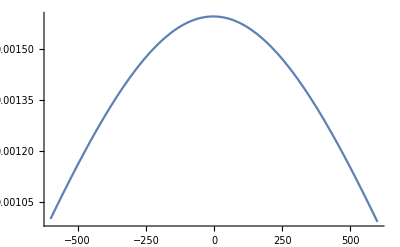
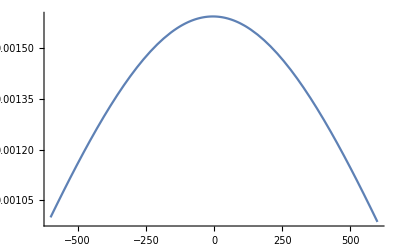
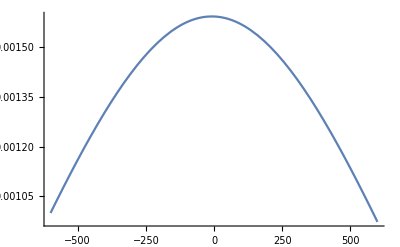
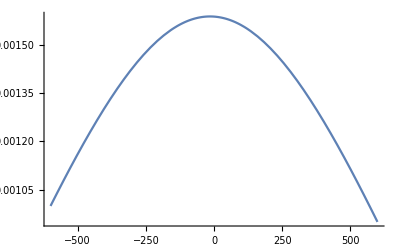
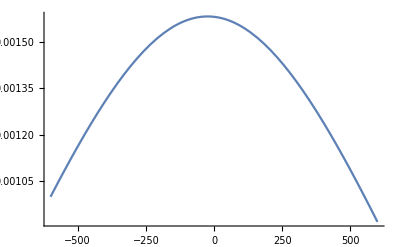
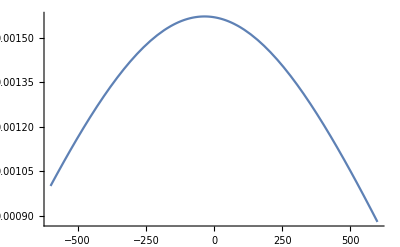
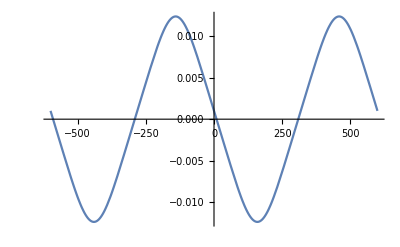
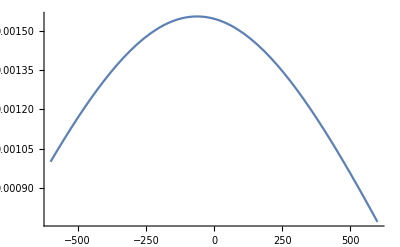

```mathematica
PlotList
```

Append::normal: Nonatomic expression expected at position TraditionalForm`1 in TraditionalForm`.

$RecursionLimit::reclim: Recursion depth of TraditionalForm`1024 exceeded.

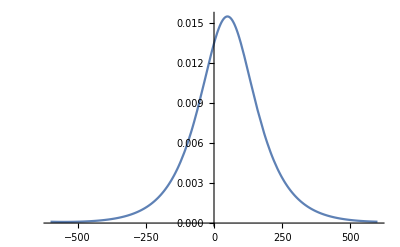

```mathematica
xmax=600;
xmin=-600;
y0=0.0001;
y1=0.0001;
EE=-0.00012;
Clear[error,y,x,c];
error[c_?NumericQ]:=(y[xmax]-y1)/.NDSolve[{-y''[x]-y[x]^3/(1+y[x]^2)==EE y[x],y[xmin]==y0,y'[xmin]==c},y,{x,xmin,xmax},AccuracyGoal->10,PrecisionGoal->30][[1]];
c0=c/.FindRoot[error[c],{c,0}];

soln=NDSolve[{-y''[x]-y[x]^3/(1+y[x]^2)==-0.00012y[x],y[xmin]==y0,y'[xmin]==c0},y,{x,xmin,xmax},AccuracyGoal->10,PrecisionGoal->30][[1]];

SolitonList=Append[SolitonList,soln];
Plot[y[x]/.soln//Evaluate,{x,xmin,xmax},PlotRange->All]
```

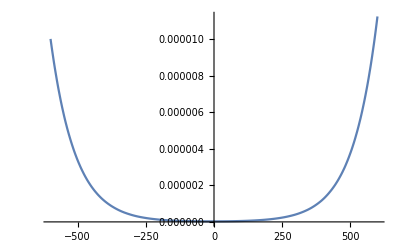

```mathematica
xmin=-600;
xmax=600;
sols=First[NDSolve[{-y''[x]-y[x]^3/(1+y[x]^2)==-0.00012y[x],y[xmin]==y[xmax]==0.00001},y,{x,xmin,xmax},Method->{"Shooting"}]];
Plot[Evaluate[y[x]/.sols],{x,xmin,xmax}]
```

```mathematica
xmax=9600;
xmin=-xmax;
IConds={ψ[0]==0.005310221,ψ'[0]==0};
Sol[EE_]:=NDSolve[
Join[{-ψ''[x]-ψ[x]^3/(1+ψ[x]^2)-EE ψ[x]==0},IConds],ψ,{x,xmin,xmax}]
ψx[EE_?NumericQ,x_]:=ψ[x]/.Sol[EE][[1]]
```

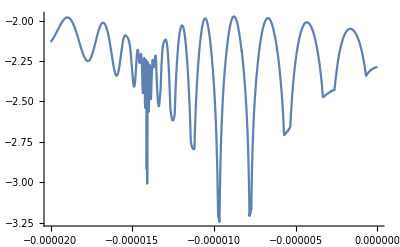

```mathematica
Plot[Log10[Abs[ψx[EE,xmax]]+Abs[ψx[EE,xmax 0.9]]],{EE,-0.00002,0},PlotRange->All]
```

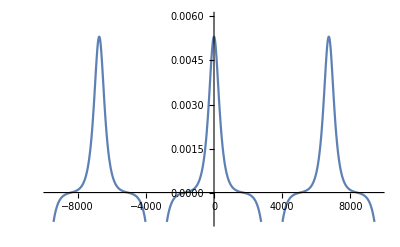

```mathematica
xMax=9600;xMin=-xMax;
Plot[Evaluate[ψx[-0.00001409942,x]],{x,xMin,xMax},PlotRange->{-0.001,0.006}]
```

```mathematica
xmax=600;
xmin=-xmax;
y0=0.0001;
y1=0.0001;
(*IConds={y[xmin]==0.0001,y'[xmin]==0};*)

Clear[error,y,x,c];
error[c_?NumericQ,EE_]:=(y[xmax]-y1)/.NDSolve[{-y''[x]-y[x]^3/(1+y[x]^2)==EE y[x],y[xmin]==y0,y'[xmin]==c},y,{x,xmin,xmax},AccuracyGoal->10,PrecisionGoal->30][[1]];
c0[EE_]:=c/.FindRoot[error[c,EE],{c,0}];

Sol[EE_]:=NDSolve[{-y''[x]-y[x]^3/(1+y[x]^2)==EE y[x],y[xmin]==y0,y'[xmin]==c0[EE]},y,{x,xmin,xmax},AccuracyGoal->10,PrecisionGoal->30];
yx[EE_?NumericQ,x_]:=y[x]/.Sol[EE][[1]]
```

```mathematica
Plot[Log[Abs[yx[EE,xmax]]],{EE,-0.0002,0.00009}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`MachinePrecision digits of working precision to meet these tolerances.

$Aborted

```mathematica
A=6.25 10^15 0.75/50 10^7 5
```

4.6875×10^21

```mathematica
B=6.25 10^15 1.3/30 10^7 10
```

2.70833×10^22

```mathematica
B/A
```

3.46667

```mathematica
W=J/s=V C/s = V A
```

```mathematica
1.3/0.75 10/5 50/30
```

5.77778

```mathematica
27.0833/4.6875
```

5.77777

```mathematica
1/1.602176565 10^19
```

6.24151×10^18

```mathematica
AA=NSolve[{-1.411184486==a 0.005312646+b,-1.411193639==a 0.0053126629535+b},{a,b}];
```

```mathematica
aa=a/.AA[[1,1]];
bb=b/.AA[[1,2]];
```

```mathematica
N[aa uL+bb/.uL->0.00532,15]
```

-1.41515